```mathematica
f[s_, a_, b_]:=128 + 64*IntegerPart[(s+a)/b]
f2[x_,  b_]:=If[b==1,128+ 64x,128 + 64*Ceiling[x/b]]
```

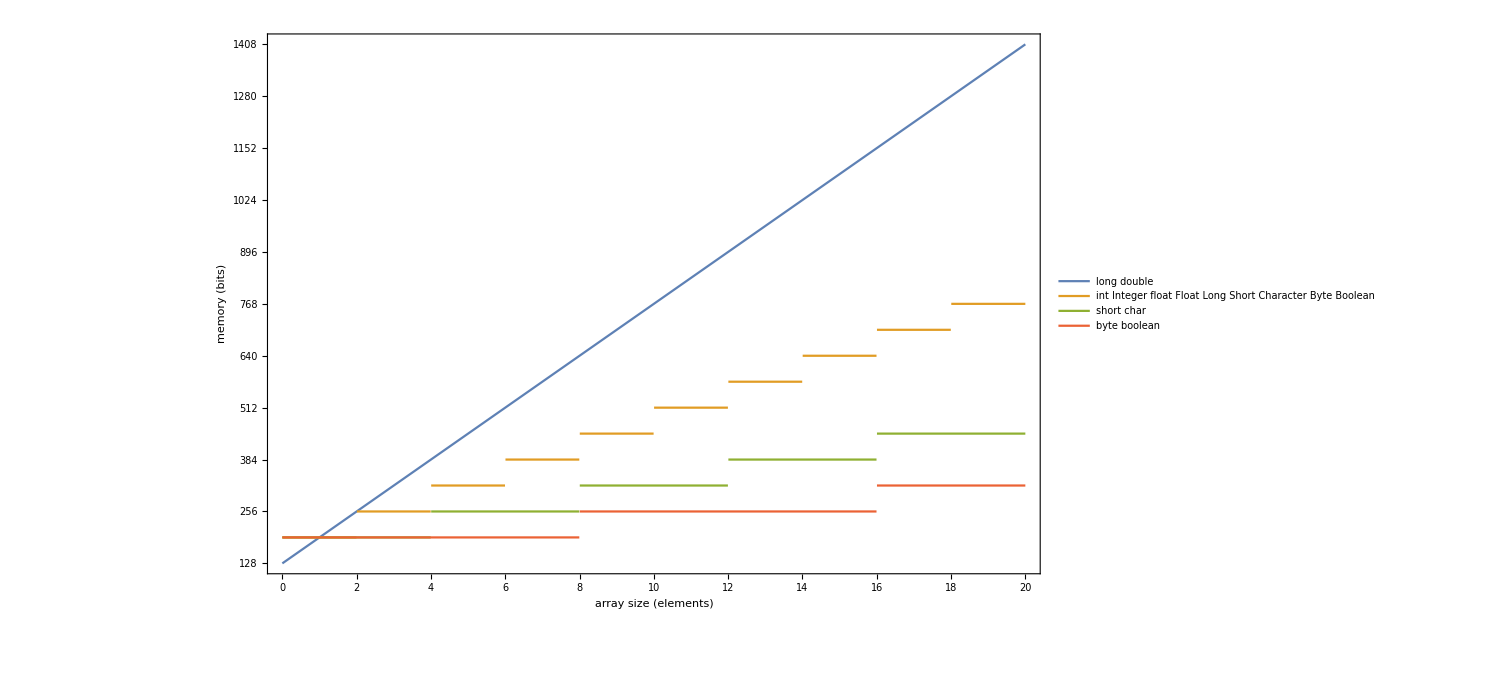

```mathematica
max = 20;
plot = Plot[{ f2[x, 1],f2[x, 2], f2[x,  4], f2[x,  8]},{x,0,max},PlotLegends->{Text[Style["long double", 20]],Text[Style["int Integer\nfloat Float\nLong Short\nCharacter\nByte Boolean", 20]],  Text[Style["short char", 20]], Text[Style["byte boolean",20]]}, AxesLabel->None,Frame->{{True,False},{True,False}},FrameTicks->{Table[i, {i, 0, max, 1}],Table[128 +8*i, {i, 0, 8*max, 8}]},
FrameLabel->{{Text[Style["memory  (bits)",20]],None},{Text[Style["array size (elements)", 20]], None}},ImageSize->1100]
```

```mathematica
Export["f:\\Users\\Andrea\\Desktop\\plot-memory-400.gif", plot, ImageSize->400, ImageResolution-> 300]
Export["f:\\Users\\Andrea\\Desktop\\plot-memory.gif", plot, ImageSize->1000, ImageResolution-> 300]
```

f:\Users\Andrea\Desktop\plot-memory-400.gif

f:\Users\Andrea\Desktop\plot-memory.gif

```mathematica
SystemOpen["f:\\Users\\Andrea\\Desktop\\plot-memory-1000.gif"]
```

```mathematica
SystemOpen["plot-memory-1000.gif"]
```

```mathematica
SystemOpen["plot-memory.gif"]
```

```mathematica
SystemOpen["plot-memory.gif"]
```

```mathematica
SystemOpen["plot-memory.png"]
```

```mathematica
Table[128 +64*i, {i, 0, 10}]
```

{128,192,256,320,384,448,512,576,640,704,768}

```mathematica
max = 18
```

18

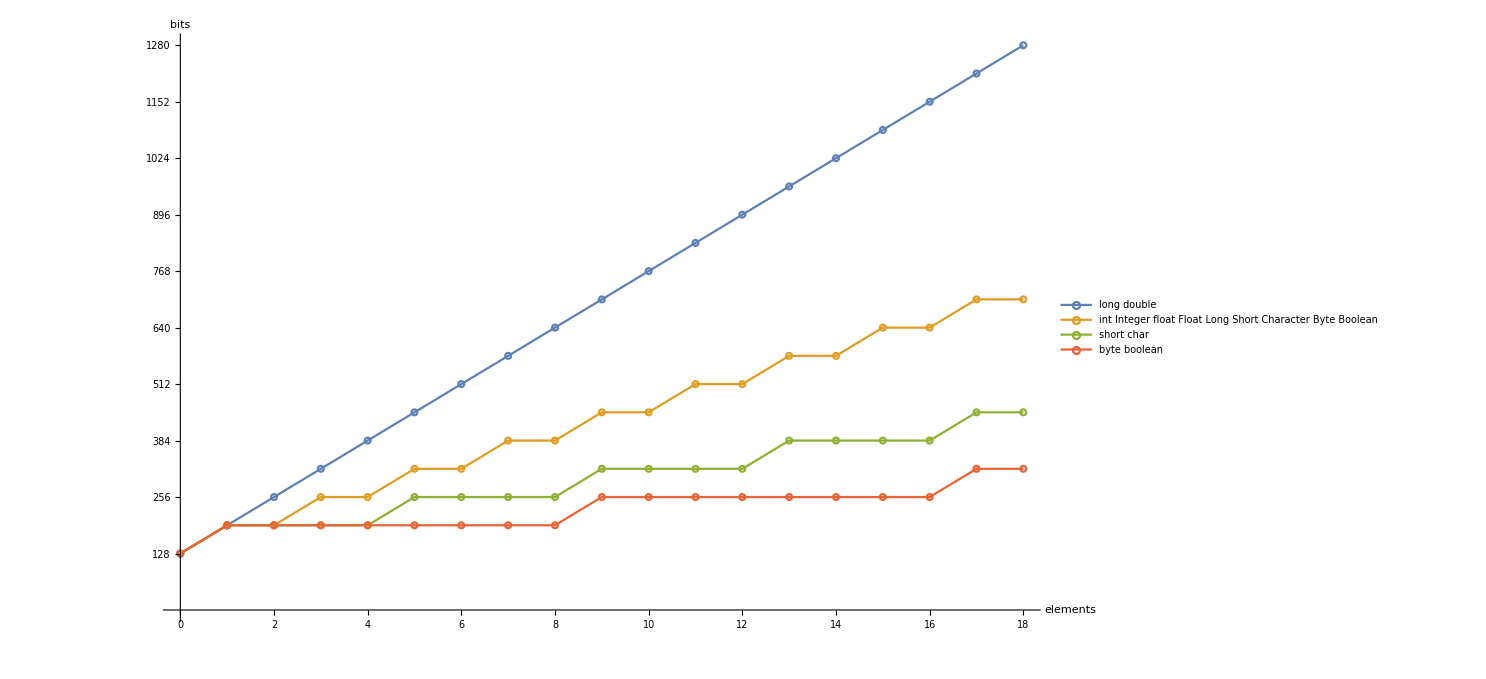

```mathematica
plot= ListPlot[{Table[{n, f2[n, 1]}, {n , 0, max}], Table[{n, f2[n, 2]}, {n , 0, max}],Table[{n, f2[n, 4]}, {n , 0, max}],Table[{n, f2[n,  8]}, {n , 0, max}] },PlotMarkers -> {Graphics[{Circle[]},ImageSize->6]},Joined->True,PlotLegends->{Text[Style["long double", 20]],Text[Style["int Integer\nfloat Float\nLong Short\nCharacter\nByte Boolean", 20]],  Text[Style["short char", 20]], Text[Style["byte boolean",20]]},Axes-> True, Ticks->{Table[i, {i, 0, max, 1}],Table[128 +64*i, {i, 0, max, 1}]},
AxesLabel->{ Text[Style["elements", 20]],Text[Style["bits",20]]},ImageSize->1100]
```

```mathematica
Export["f:\\Users\\Andrea\\Desktop\\plot-memory.gif", plot, ImageSize->1000, ImageResolution-> 300]
```

f:\Users\Andrea\Desktop\plot-memory.gif

```mathematica
SystemOpen["f:\\Users\\Andrea\\Desktop\\plot-memory.gif"]
```

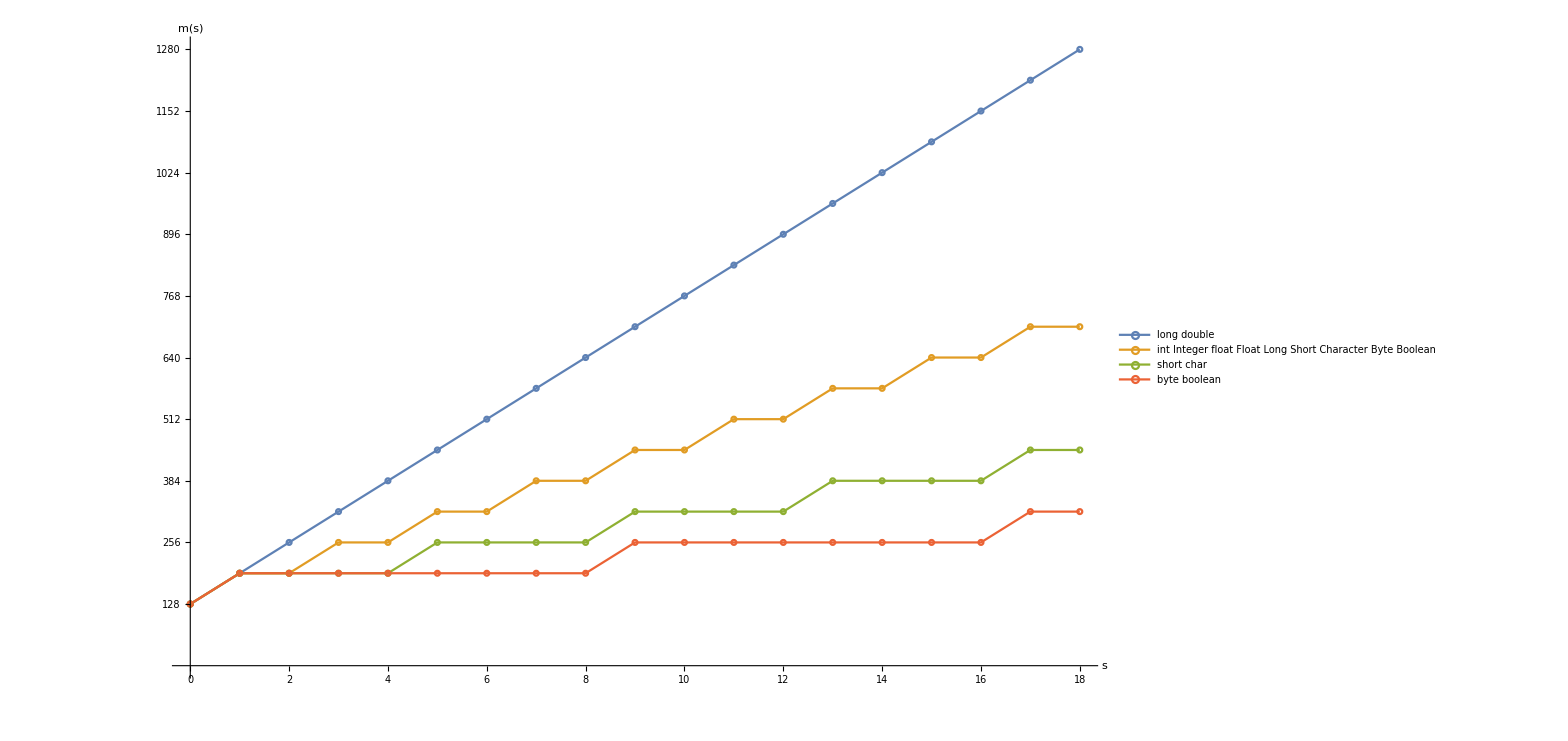

```mathematica
ListPlot[{Table[{n, f2[n, 1]}, {n , 0, max}], Table[{n, f2[n, 2]}, {n , 0, max}],Table[{n, f2[n, 4]}, {n , 0, max}],Table[{n, f2[n,  8]}, {n , 0, max}] },PlotMarkers -> {Graphics[{Circle[]},ImageSize->5]},Joined->True,Axes -> {0, 0},PlotLegends->{Text[Style["long double", 20]],Text[Style["int Integer\nfloat Float\nLong Short\nCharacter\nByte Boolean", 20]],  Text[Style["short char", 20]], Text[Style["byte boolean",20]]}, Ticks->{Table[i, {i, 0, max, 1}],Table[128 +64*i, {i, 0, max, 1}]},
AxesLabel->{Text[Style["s", 20]], Text[Style["m(s)",20]]},ImageSize->1200]
```

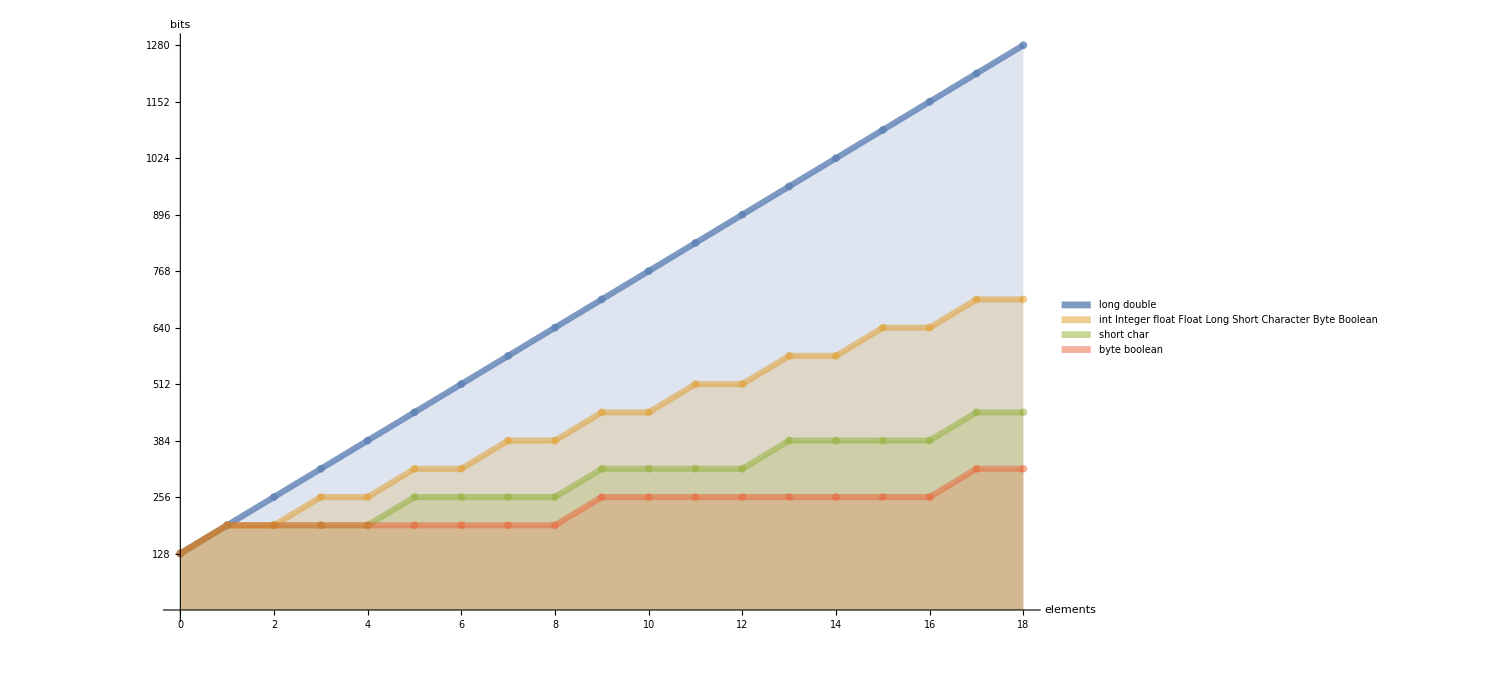

```mathematica
axeStyle = Directive[Black, 20, Thickness[0.003]];
lineStyle[o_]:= Directive[Opacity[o],Thickness[0.004]];
plot2 = ListPlot[{Table[{n, f2[n, 1]}, {n , 0, max}], Table[{n, f2[n, 2]}, {n , 0, max}],Table[{n, f2[n, 4]}, {n , 0, max}],Table[{n, f2[n,  8]}, {n , 0, max}] },PlotMarkers -> {Graphics[{Disk[]},ImageSize->8]},Joined->True, PlotLegends->Placed[SwatchLegend[{Text[Style["long double", 20]],Text[Style["int Integer float Float Long Short Character Byte Boolean", 20]],  Text[Style["short char", 20]], Text[Style["byte boolean",20]]}],{0.3,0.8}],Axes-> True, AxesStyle ->{ axeStyle, axeStyle},Ticks->{Table[i, {i, 0, max, 1}],Table[128 +64*i, {i, 0, max, 1}]},PlotStyle->{lineStyle[0.8], lineStyle[0.5],lineStyle[0.5],lineStyle[0.5]},FillingStyle->Opacity[0.2],Filling->Axis,
AxesLabel->{ Text[Style["elements", 20]],Text[Style["bits",20]]},ImageSize->1100]
```

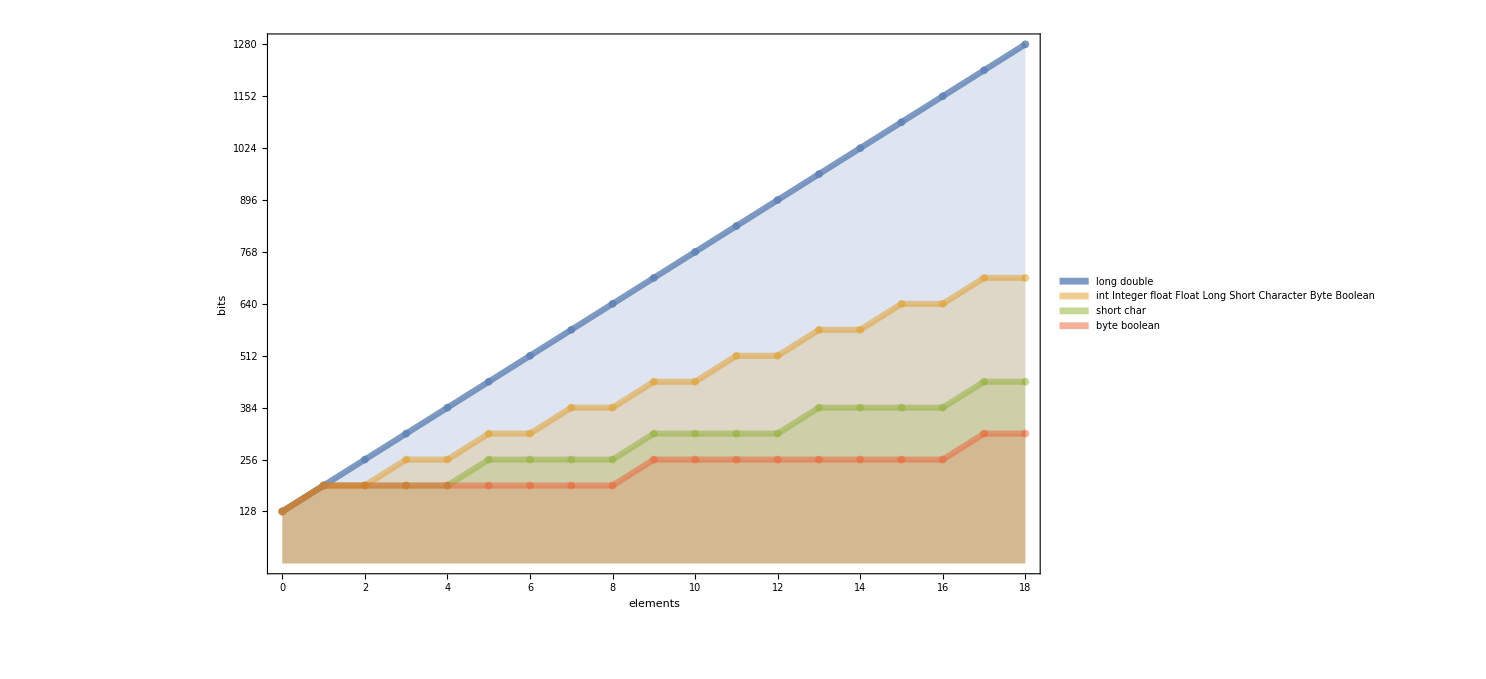

```mathematica
plot3= ListPlot[{Table[{n, f2[n, 1]}, {n , 0, max}], Table[{n, f2[n, 2]}, {n , 0, max}],Table[{n, f2[n, 4]}, {n , 0, max}],Table[{n, f2[n,  8]}, {n , 0, max}] },PlotMarkers -> {Graphics[{Disk[]},ImageSize->8]},Joined->True, PlotLegends->Placed[SwatchLegend[{Text[Style["long double", 20]],Text[Style["int Integer float Float Long Short Character Byte Boolean", 20]],  Text[Style["short char", 20]], Text[Style["byte boolean",20]]}],{0.28,0.85}],Axes-> False, Frame->{{True, False},{True, False}},FrameStyle ->{ axeStyle, axeStyle},FrameTicks->{Table[i, {i, 0, max, 1}],Table[128 +64*i, {i, 0, max, 1}]} ,PlotRangePadding->0,PlotStyle->{lineStyle[0.8], lineStyle[0.5],lineStyle[0.5],lineStyle[0.5]},FillingStyle->Opacity[0.2],Filling->Axis,
FrameLabel->{ Text[Style["elements", 20]],Text[Style["bits",20]]},ImageSize->1100]
```

```mathematica
Export["f:\\Users\\Andrea\\Documents\\baeldung\\plot-memory-bits.gif", plot3, ImageSize->1010, ImageResolution-> 300]
```

f:\Users\Andrea\Documents\baeldung\plot-memory-bits.gif

```mathematica
SystemOpen["f:\\Users\\Andrea\\Desktop\\plot-memory-bits.gif"]
```